# All Pairs Shortest Paths

## Definition

Let G=(V,E) be a directed graph with n vertices. Let cost be a cost adjacency matrix for G such that cost(i,i)=0,1≤i≤n. Then cost(i,j) is the length (or cost) of edge ⟨i,j⟩ if ⟨i,j⟩∈E(G) and cost(i,j)=∞ if i≠j and ⟨i,j⟩∉E(G).

The all pairs shortest path problem is to determine a matrix A such that A(i,j) is the length of the shortest path from i to j.

This problem satisfies the oprtimality principle.

Time complexity is Θ(n^3).

{{0,4,6},{5,0,2},{3,7,0}}

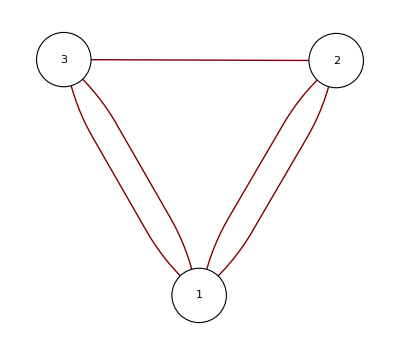

```mathematica
M[0]=({{0, 4, 11}, {6, 0, 2}, {3, ∞, 0}});
t=Flatten[DeleteCases[Table[If[M[0][[i,j]]==Infinity,Null,{i->j, M[0][[i,j]]}],{i,1,3},{j,1,3}],Null,2],1];
cost=M[0];
M[k_]:=Table[Min[If[k==0,cost[[i,j]],M[k-1][[i,j]]],M[k-1][[i,k]]+M[k-1][[k,j]]],{i,3},{j,3}];
M[3]
GraphPlot[t,DirectedEdges->True, VertexLabeling->True, EdgeLabeling->True, SelfLoopStyle->None, VertexRenderingFunction->({White,EdgeForm[Black],Disk[#,.1],Black,Text[#2,#1]}&)]
```

## Exercises

1. (a) Yes (b) The length gets reduced each time a loop occurs and thus the length can be reduced arbitrarily.
3. (a) A^+=(1 | 1 | 1 | 1
1 | 1 | 1 | 1
1 | 1 | 1 | 1
1 | 1 | 1 | 1)      A^*=(1 | 1 | 1 | 1
1 | 1 | 1 | 1
1 | 1 | 1 | 1
1 | 1 | 1 | 1)      A=(0 | 1 | 0 | 1
0 | 0 | 1 | 0
1 | 0 | 0 | 0
0 | 0 | 1 | 0)
(b) A^0=(1 | 1 | 0 | 1
0 | 1 | 1 | 0
1 | 0 | 1 | 0
0 | 0 | 1 | 1)=A∨(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1)
(c) A^k(i, j) = [A^(k-1)(i, k) ∧ A^(k-1)(k, j)]∨A^(k-1)(i,j)
(d) In place editing of A^k(i,j) will result in space requirement of Ο(n^2) and time complexity will be Ο(n^3) since A^* can be calculated only when k=n.
(e) Check with above given values.